## Circuit 1: Serial LRC Circuit

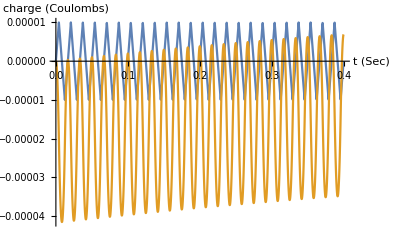

```mathematica
Clear[V,t]
TMax=0.4;
{R1,C2,L3}={100.,0.01,0.01};
V[t_]:=TriangleWave[60 t]
qSol=NDSolveValue[{
V[t]+ R1 q'[t]+ q[t]/C2 + L3 q''[t]==0,
q[0]==0,q'[0]==0},
q,{t, 0, TMax}];
Plot[{0.00001 V[t],qSol[t]}, {t, 0, TMax},
AxesLabel->{"t (Sec)","charge (Coulombs)"}]
```

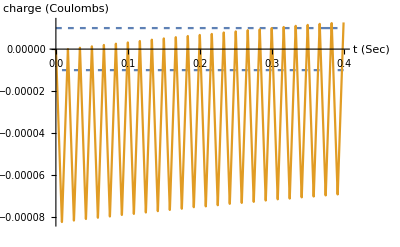

```mathematica
Clear[V,t]
TMax=0.4;
{R1,C2,L3}={100.,0.01,0.01};
V[t_]:=SquareWave[60 t]
qSol=NDSolveValue[{
V[t]+ R1 q'[t]+ q[t]/C2 + L3 q''[t]==0,
q[0]==0,q'[0]==0},
q,{t, 0, TMax}];
Plot[{0.00001 V[t],qSol[t]}, {t, 0, TMax},
AxesLabel->{"t (Sec)","charge (Coulombs)"}]
```

## Circuit 2: Two Loop LRC Circuit

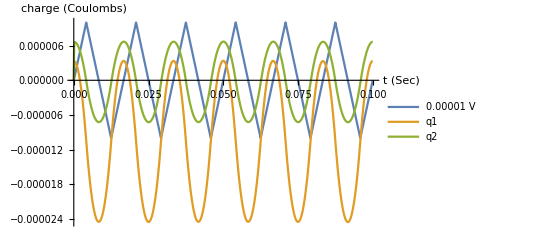

```mathematica
Clear[V,t]
TMax=0.1;
{R1,R2,C3,L4, R5, C6}={100.,100.0,0.1,0.01,100.0, 0.1};
V[t_]:=TriangleWave[60 t]
{q1Sol,q2Sol}=NDSolveValue[{
V[t]+ R1 q1'[t]+R2 (q1'[t]-q2'[t])+ q1[t]/C6 ==0,
q2[t]/C3 + L4 q2''[t]+ R2 (q2'[t]-q1'[t])+R5 q2'[t]==0,
q1[0]==0,q2[0]==0,q2'[0]==0.1},
{q1,q2},{t, 0, TMax}];
Plot[{0.00001 V[t],q1Sol[t],q2Sol[t]}, {t, 0, TMax},
AxesLabel->{"t (Sec)","charge (Coulombs)"},
PlotLegends->{"0.00001 V","q1","q2"}]
```